```mathematica
dataset = Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}];
```

```mathematica
dataset1 =Flatten[StringCases[dataset,"http://www-groups.dcs.st-and.ac.uk/history/Biographies/"~~__]];
```

```mathematica
dataset2 = Import[#,"Text"]&/@dataset1
```

{6706,8997,7335,26071,13189,8342,33967,14134,17034,14494,2755,22932,25623,32677,25710,28993,20588,22485,15680,26426,25808}
 |  |  |  |

## HTML Parser

```mathematica
TemplateApply;

$mapping=Reverse[Normal[Templating`HTML`PackagePrivate`$SafeHTMLEntities],{2}];

htmlToText[txt_String]:=StringReplace[txt,$mapping]
```

```mathematica
htmls= Map[htmlToText,dataset2]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,2755,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

## Exporting List of HTMLs

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables

```mathematica
Export["htmlbiographies.mx",htmls,"MX"]
```

htmlbiographies.mx

```mathematica
Export["listURLs.mx",dataset1,"MX"]
```

listURLs.mx

```mathematica
htmlList = Import["htmlbiographies.mx"]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,13304,28030,15557,14923,2747,18501,21861,14801,22484,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

```mathematica
Export["Biography1.m",dataset2]
```

```mathematica
ClearAll[x]
```

```mathematica
fullNames =StringCases[htmlList,"<h1>"~~x__~~"</h1>"->x];
```

```mathematica
birthdate= StringCases[htmlList, "Born:<font color=\"green\"> "~~Shortest[y__]~~"<br>"->y];
```

```mathematica
deathdate=StringCases[htmlList, "<font color=\"purple\">"~~Shortest[z__]~~"</font>"->z];
```

```mathematica
ClearAll[a]
```

```mathematica
StringCases[htmlList[[22]],"../Mathematicians/"~~Shortest[a__]~~".html"->a]
```

{Plato,Plato,Plato,Plato,Theodorus,Theodorus,Plato,Plato,Plato,Plato,Theodorus,Theodorus,Plato,Plato,Plato,Plato,Euclid,Euclid,Pappus,Pappus,Euclid,Euclid,Euclid,Euclid,Pythagoras,Pythagoras,Pappus,Pappus,Theodorus,Theodorus,Heath,Heath,Pappus,Pappus,Eudemus,Eudemus,Van_der_Waerden,Van_der_Waerden,Van_der_Waerden,Van_der_Waerden,Euclid,Euclid,Euclid,Euclid,Plato,Plato,Theodorus,Theodorus,Theodorus,Theodorus,Eudoxus,Eudoxus,Euclid,Euclid,Geminus,Geminus,Plato,Plato,Pappus,Pappus}

## Get Rid of JS stuff

```mathematica
Counts[Flatten[(StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a](StringContainsQ[#," "]&)->Nothing)]]
```

Counts::invl: The argument … is not a list.

Counts[{{},{1},2771,{1},{McMullen (StringContainsQ[#1, ]&),McMullen (StringContainsQ[#1, ]&),McMullen (StringContainsQ[#1, ]&),17,Fields (StringContainsQ[#1, ]&),Fields (StringContainsQ[#1, ]&)}}→7]
 |  |  |  |

```mathematica
"De_Morgan',550,800); return false;\">George Boole</m></font>\n</article><hr>\n<b><a href = \"../References/Walsh"
```

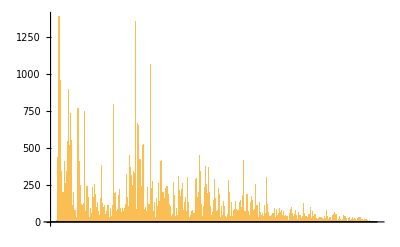

```mathematica
BarChart[Counts[Flatten[StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a]]]]
```

## Counting String Length

```mathematica
ClearAll[x];

getBodyBio [ htmlString_String ] := StringCases[ htmlString ,
                                                "<article>" ~~ Shortest[ x__ ] ~~ "</article>" -> x
                                                ];
                                                
deleteHtmlElements [ htmlString_String ] := StringDelete[
                                                          getBodyBio[ htmlString ],
                                                         "<"~~Shortest[__]~~">" 
                                                         ];
                                                         
numberSentences [ htmlString_String ] := Length@First@TextCases[ deleteHtmlElements [ htmlString ] , "Sentence"];

numberWords [ htmlString_String ] := Length@First@TextCases[ deleteHtmlElements [ htmlString ] , "Word"];
```

```mathematica
numberSentences[htmlList[[2]]]
```

22

```mathematica
numberWords[htmlList[[2]]]
```

477

```mathematica
StringCases[htmlList[[2]],"<article>"~~Shortest[x__]~~"</article>"->x];
```

{To write a biography of <b>Baudhayana</b> is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras. We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.
<p>
He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like <a href="../Mathematicians/Ahmes.html" onclick="javascript:win1('../Mathematicians/Ahmes.html',400,400); return false;">Ahmes</a>. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. 
<p>
The mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices. It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman. He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. 
<p>
The Sulbasutras are discussed in detail in the article <a href="../HistTopics/Indian_sulbasutras.html">Indian Sulbasutras</a>. Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.
<p>
The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown. Quadratic equations of the forms <i>ax</i><sup>2</sup> = <i>c</i> and <i>ax</i><sup>2</sup> + <i>bx</i> = <i>c</i> appear.
<p>
Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes. Constructions are given which are equivalent to taking &#960; equal to <sup>676</sup>/<sub>225</sub> (where <sup>676</sup>/<sub>225</sub> = 3.004), <sup>900</sup>/<sub>289</sub> (where <sup>900</sup>/<sub>289</sub> = 3.114) and to <sup>1156</sup>/<sub>361</sub> (where <sup>1156</sup>/<sub>361</sub> = 3.202). None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.
<p>
An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra. The Sanskrit text gives in words what we would write in symbols as<br>
<div style="margin:1em 0 1em 40px";>
&#8730;2 = 1 + <sup>1</sup>/<sub>3</sub> + <sup>1</sup>/<sub>(3&#215;4)</sub> - <sup>1</sup>/<sub>(3&#215;4&#215;34)</sub> = <sup>577</sup>/<sub>408</sub> <br>
</div>
which is, to nine places, 1.414215686. This gives &#8730;2 correct to five decimal places. This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described. If the approximation was given as <br>
<div style="margin:1em 0 1em 40px";>
&#8730;2 = 1 + <sup>1</sup>/<sub>3</sub> + <sup>1</sup>/<sub>(3&#215;4)</sub><br>
</div>
then the error is of the order of 0.002 which is still more accurate than any of the values of &#960;. Why then did Baudhayana feel that he had to go for a better approximation?
<p>
See the article <a href="../HistTopics/Indian_sulbasutras.html">Indian Sulbasutras</a> for more information.
<p>
<p><font color=purple><b>Article by:</b> <i>J J O'Connor</i> and <i>E F Robertson</i></font>
}

```mathematica
getBodyBio[htmlList[[2]]]
```

```mathematica
StringDelete[getBodyBio[htmlList[[2]]],"<"~~Shortest[__]~~">"]
```

```mathematica
StringDelete[%,"<"~~Shortest[__]~~">"]
```

{To write a biography of Baudhayana is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras. We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.

He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like Ahmes. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. 

The mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices. It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman. He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. 

The Sulbasutras are discussed in detail in the article Indian Sulbasutras. Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.

The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown. Quadratic equations of the forms ax2 = c and ax2 + bx = c appear.

Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes. Constructions are given which are equivalent to taking &#960; equal to 676/225 (where 676/225 = 3.004), 900/289 (where 900/289 = 3.114) and to 1156/361 (where 1156/361 = 3.202). None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.

An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra. The Sanskrit text gives in words what we would write in symbols as

&#8730;2 = 1 + 1/3 + 1/(3&#215;4) - 1/(3&#215;4&#215;34) = 577/408 

which is, to nine places, 1.414215686. This gives &#8730;2 correct to five decimal places. This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described. If the approximation was given as 

&#8730;2 = 1 + 1/3 + 1/(3&#215;4)

then the error is of the order of 0.002 which is still more accurate than any of the values of &#960;. Why then did Baudhayana feel that he had to go for a better approximation?

See the article Indian Sulbasutras for more information.

Article by: J J O'Connor and E F Robertson
}

```mathematica
TextCases[%297,"Sentence"]
```

```mathematica
{{"To write a biography of Baudhayana is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras.","We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.","He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like Ahmes.","He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes.","Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. \n\nThe mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices.","It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman.","He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. \n\nThe Sulbasutras are discussed in detail in the article Indian Sulbasutras.","Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.","The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown.","Quadratic equations of the forms ax2 = c and ax2 + bx = c appear.","Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes.","Constructions are given which are equivalent to taking &#960; equal to 676/225 (where 676/225 = 3.004), 900/289 (where 900/289 = 3.114) and to 1156/361 (where 1156/361 = 3.202).","None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.","An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra.","The Sanskrit text gives in words what we would write in symbols as\n\n&#8730;2 = 1 + 1/3 + 1/(3&#215;4)","- 1/(3&#215;4&#215;34) = 577/408 \n\nwhich is, to nine places, 1.414215686.","This gives &#8730;2 correct to five decimal places.","This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described.","If the approximation was given as \n\n&#8730;2 = 1 + 1/3 + 1/(3&#215;4)\n\nthen the error is of the order of 0.002 which is still more accurate than any of the values of &#960;.","Why then did Baudhayana feel that he had to go for a better approximation?","See the article Indian Sulbasutras for more information.","Article by: J J O'Connor and E F Robertson\n"}}[[1]]//Length
```

22

## Wikipedia Data

```mathematica
ClearAll[b]
```

```mathematica
fullNames[[30;;40]]
```

{{Menaechmus },{Aristaeus the Elder },{Callippus of Cyzicus },{Autolycus of Pitane },{Eudemus of Rhodes },{Euclid of Alexandria },{Aristarchus of Samos },{Archimedes of Syracuse },{Chrysippus of Soli },{Conon of Samos },{Nicomedes }}

```mathematica
findWikiData[name_]:=If[Length[WikipediaSearch[name]]&<2,WikipediaSearch[name]&,Interpreter["Person"][name]&]
```

```mathematica
findWikiData[#]&/@fullNames[[30;;40]]
```

{If[Length[WikipediaSearch[{Menaechmus }]]&<2,WikipediaSearch[{Menaechmus }]&,Interpreter[Person][{Menaechmus }]&],If[Length[WikipediaSearch[{Aristaeus the Elder }]]&<2,WikipediaSearch[{Aristaeus the Elder }]&,Interpreter[Person][{Aristaeus the Elder }]&],If[Length[WikipediaSearch[{Callippus of Cyzicus }]]&<2,WikipediaSearch[{Callippus of Cyzicus }]&,Interpreter[Person][{Callippus of Cyzicus }]&],If[Length[WikipediaSearch[{Autolycus of Pitane }]]&<2,WikipediaSearch[{Autolycus of Pitane }]&,Interpreter[Person][{Autolycus of Pitane }]&],If[Length[WikipediaSearch[{Eudemus of Rhodes }]]&<2,WikipediaSearch[{Eudemus of Rhodes }]&,Interpreter[Person][{Eudemus of Rhodes }]&],If[Length[WikipediaSearch[{Euclid of Alexandria }]]&<2,WikipediaSearch[{Euclid of Alexandria }]&,Interpreter[Person][{Euclid of Alexandria }]&],If[Length[WikipediaSearch[{Aristarchus of Samos }]]&<2,WikipediaSearch[{Aristarchus of Samos }]&,Interpreter[Person][{Aristarchus of Samos }]&],If[Length[WikipediaSearch[{Archimedes of Syracuse }]]&<2,WikipediaSearch[{Archimedes of Syracuse }]&,Interpreter[Person][{Archimedes of Syracuse }]&],If[Length[WikipediaSearch[{Chrysippus of Soli }]]&<2,WikipediaSearch[{Chrysippus of Soli }]&,Interpreter[Person][{Chrysippus of Soli }]&],If[Length[WikipediaSearch[{Conon of Samos }]]&<2,WikipediaSearch[{Conon of Samos }]&,Interpreter[Person][{Conon of Samos }]&],If[Length[WikipediaSearch[{Nicomedes }]]&<2,WikipediaSearch[{Nicomedes }]&,Interpreter[Person][{Nicomedes }]&]}

```mathematica
Interpreter["Person"][{"Isaac Newton","Nicomedes "}]
```

{Isaac Newton,Nicomedes}

Menaechmus

"Isaac Newton"

```mathematica
WikipediaData["Nicomedes","ArticleWikicode"]
```

'''Nicomedes'''  may refer to:
*[[Nicomedes (mathematician)]], ancient Greek mathematician who discovered the conchoid
*Nicomedes, uncle of the 19th Agiad [[Sparta]]n king [[Pleistoanax]], commanded the Spartan army at the [[Battle of Tanagra (457 BC)|Battle of Tanagra]]
*[[Saint Nicomedes]], Martyr of unknown era, whose feast is observed 15 September

Four kings of Bithynia in Anatolia, 3rd–1st century BC:
*[[Nicomedes I of Bithynia]], ruled 278–255 BC
*[[Nicomedes II of Bithynia]], 149–127 BC
*[[Nicomedes III of Bithynia]], 127–94 BC
*[[Nicomedes IV of Bithynia]], 94–74 BC

{{hndis}}

```mathematica
WikipediaData[Entity["Person","Nicomedes::2c234"],"ArticleWikicode"]
```

[[Image:Conchoid of Nicomedes.png|200px|right|thumb|[[Conchoid (mathematics)|Conchoid]]s of line with common center.]]
[[File:Nicomedes.gif|thumb|Conchoid of Nicomedes drawn by an apparatus illustrated in Eutocius' Commentaries on the works of Archimedes]]
'''Nicomedes''' ({{IPAc-en|ˌ|n|ɪ|k|ə|ˈ|m|iː|d|iː|z}}; {{lang-grc-gre|Νικομήδης}}; c. 280 – c. 210 BC) was an [[ancient Greek]] [[mathematician]].

== Life and work ==
Almost nothing is known about Nicomedes' life apart from references in his works. Studies have stated that Nicomedes was born in about 280 BC and died in about 210 BC. It is known that he lived around the time of [[Eratosthenes]] or after, because he criticized Eratosthenes' method of [[doubling the cube]]. It is also known that [[Apollonius of Perga]] called a curve of his creation a "sister of the [[Conchoid (mathematics)|conchoid]]", suggesting that he was naming it after Nicomedes' already famous curve. Consequently, it is believed that Nicomedes lived after [[Eratosthenes]] and before [[Apollonius of Perga]].

Like many geometers of the time, Nicomedes was engaged in trying to solve the problems of doubling the cube and [[trisecting the angle]], both problems we now understand to be impossible using the tools of classical [[geometry]]. In the course of his investigations, Nicomedes created the [[Conchoid (mathematics)|conchoid]]<ref>{{cite EB1911|wstitle=Conchoid|volume=6|pages=826–827}}</ref> of Nicomedes; a discovery that is contained in his famous work entitled ''On conchoid lines''. Nicomedes discovered three distinct types of conchoids, now unknown. [[Pappus of Alexandria|Pappus]] wrote: "Nicomedes trisected any rectilinear angle by means of the conchoidal curves, the construction, order and properties of which he handed down, being himself the discoverer of their peculiar character".<ref name="Heath"/>

Nicomedes also used the [[Hippias]]' [[quadratrix]] to [[squaring the circle|square the circle]], since according to Pappus, "For the squaring of the circle there was used by Dinostratus, Nicomedes, and certain other later persons a certain curve which took its name from this property, for it is called by them square-forming".<ref name="Heath"/> [[Eutocius]] mentions that Nicomedes "prided himself inordinately on his discovery of this curve, contrasting it with Eratosthenes's mechanism for finding any number of mean proportionals, to which he objected formally and at length on the ground that it was impracticable and entirely outside the spirit of geometry".<ref name="Heath">Heath (1921)</ref>

== Citations and footnotes ==
<references/>

==References==
*[[T. L. Heath]], A History of Greek Mathematics (2 Vols.) (Oxford, 1921).
*[[G. J. Toomer]], Biography in Dictionary of Scientific Biography (New York 1970–1990).

== External links ==
* {{MacTutor Biography|id = Nicomedes}}

{{Ancient Greek mathematics}}

{{DEFAULTSORT:Nicomedes}}
[[Category:Ancient Greek mathematicians]]
[[Category:3rd-century BC Greek people]]
[[Category:3rd-century BC writers]]
[[Category:280s BC births]]
[[Category:210s BC deaths]]

```mathematica
"Euclid of Alexandria "
```

```mathematica
WikipediaSearch["Chrysippus of Soli"]
```

{Chrysippus of Soli}

```mathematica
WikipediaData["Aristaeus the Elder "]
```

```mathematica
WikipediaSearch["Title"->"Aristaeus the Elder",]
```

WikipediaSearch::invinpm: Title -> Aristaeus the Elder, Person are not valid inputs.

WikipediaSearch[Title→Aristaeus the Elder,Person]

```mathematica
wikiCodeMathematicians= Map[WikipediaData[#<>" (mathematician)","ArticleWikicode"] &,fullNames[[30;;40]]]
```

{Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],[[Image:Conchoid of Nicomedes.png|200px|right|thumb|[[Conchoid (mathematics)|Conchoid]]s of line with common center.]]
[[File:Nicomedes.gif|thumb|Conchoid of Nicomedes drawn by an apparatus illustrated in Eutocius' Commentaries on the works of Archimedes]]
'''Nicomedes''' ({{IPAc-en|ˌ|n|ɪ|k|ə|ˈ|m|iː|d|iː|z}}; {{lang-grc-gre|Νικομήδης}}; c. 280 – c. 210 BC) was an [[ancient Greek]] [[mathematician]].

== Life and work ==
Almost nothing is known about Nicomedes' life apart from references in his works. Studies have stated that Nicomedes was born in about 280 BC and died in about 210 BC. It is known that he lived around the time of [[Eratosthenes]] or after, because he criticized Eratosthenes' method of [[doubling the cube]]. It is also known that [[Apollonius of Perga]] called a curve of his creation a "sister of the [[Conchoid (mathematics)|conchoid]]", suggesting that he was naming it after Nicomedes' already famous curve. Consequently, it is believed that Nicomedes lived after [[Eratosthenes]] and before [[Apollonius of Perga]].

Like many geometers of the time, Nicomedes was engaged in trying to solve the problems of doubling the cube and [[trisecting the angle]], both problems we now understand to be impossible using the tools of classical [[geometry]]. In the course of his investigations, Nicomedes created the [[Conchoid (mathematics)|conchoid]]<ref>{{cite EB1911|wstitle=Conchoid|volume=6|pages=826–827}}</ref> of Nicomedes; a discovery that is contained in his famous work entitled ''On conchoid lines''. Nicomedes discovered three distinct types of conchoids, now unknown. [[Pappus of Alexandria|Pappus]] wrote: "Nicomedes trisected any rectilinear angle by means of the conchoidal curves, the construction, order and properties of which he handed down, being himself the discoverer of their peculiar character".<ref name="Heath"/>

Nicomedes also used the [[Hippias]]' [[quadratrix]] to [[squaring the circle|square the circle]], since according to Pappus, "For the squaring of the circle there was used by Dinostratus, Nicomedes, and certain other later persons a certain curve which took its name from this property, for it is called by them square-forming".<ref name="Heath"/> [[Eutocius]] mentions that Nicomedes "prided himself inordinately on his discovery of this curve, contrasting it with Eratosthenes's mechanism for finding any number of mean proportionals, to which he objected formally and at length on the ground that it was impracticable and entirely outside the spirit of geometry".<ref name="Heath">Heath (1921)</ref>

== Citations and footnotes ==
<references/>

==References==
*[[T. L. Heath]], A History of Greek Mathematics (2 Vols.) (Oxford, 1921).
*[[G. J. Toomer]], Biography in Dictionary of Scientific Biography (New York 1970–1990).

== External links ==
* {{MacTutor Biography|id = Nicomedes}}

{{Ancient Greek mathematics}}

{{DEFAULTSORT:Nicomedes}}
[[Category:Ancient Greek mathematicians]]
[[Category:3rd-century BC Greek people]]
[[Category:3rd-century BC writers]]
[[Category:280s BC births]]
[[Category:210s BC deaths]]}

```mathematica
Length@%203
```

40

```mathematica
Part[%203, -1]
```

'''Nicomedes'''  may refer to:
*[[Nicomedes (mathematician)]], ancient Greek mathematician who discovered the conchoid
*Nicomedes, uncle of the 19th Agiad [[Sparta]]n king [[Pleistoanax]], commanded the Spartan army at the [[Battle of Tanagra (457 BC)|Battle of Tanagra]]
*[[Saint Nicomedes]], Martyr of unknown era, whose feast is observed 15 September

Four kings of Bithynia in Anatolia, 3rd–1st century BC:
*[[Nicomedes I of Bithynia]], ruled 278–255 BC
*[[Nicomedes II of Bithynia]], 149–127 BC
*[[Nicomedes III of Bithynia]], 127–94 BC
*[[Nicomedes IV of Bithynia]], 94–74 BC

{{hndis}}

## Mental Health Disorders List

```mathematica
mentalDisorders = Import["list_of_mental_disorders.js","List"];
```

```mathematica
expandedDisorders=Join[{"fatigue","dementia"},mentalDisorders];
```

# Extracting Symbols

```mathematica
text=Import["https://en.wikipedia.org/wiki/Table_of_mathematical_symbols_by_introduction_date","Data"];
```

```mathematica
table=Dataset[Cases[text,{_,_,_,_},∞]]
```

Dataset[<>]